```mathematica
Solve[lambda*R^(lambda-1)*F*r-(R^(2*lambda)+2*R^lambda*r+r^2)==0,R]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-r^2+F lambda r R^(-1+lambda)-2 r R^lambda-R^(2 lambda)==0,R]

```mathematica
lambda=1;
```

```mathematica
Solve[lambda*R^(lambda-1)*F*r-(R^(2*lambda)+2*R^lambda*r+r^2)==0,R]
```

{{R→-√F √r-r},{R→√F √r-r}}

```mathematica
D[R^lambda/(R^lambda+r)*F-R,R]
```

-1-(F lambda R^(-1+2 lambda))/((r+R^lambda)^2)+(F lambda R^(-1+lambda))/(r+R^lambda)

```mathematica
Simplify[D[(lambda*R^(lambda-1)*F*r-(R^lambda+r)^2)/(R^lambda+r)^2,R]]
```

-(F lambda r R^(-2+lambda) (r-lambda r+(1+lambda) R^lambda))/((r+R^lambda)^3)

```mathematica
(F lambda r R^(-1+lambda)-(r+R^lambda)^2)/((r+R^lambda)^2)==-1-(F lambda R^(-1+2 lambda))/((r+R^lambda)^2)+(F lambda R^(-1+lambda))/(r+R^lambda)
```

True

```mathematica
(*resultado da primeira derivação em ordem a R bem, yay!*)
```

```mathematica
D[R^lambda/(R^lambda+r)*F-R,{R,2}]
```

-(2 F lambda^2 R^(-2+2 lambda))/((r+R^lambda)^2)+(F (-1+lambda) lambda R^(-2+lambda))/(r+R^lambda)+F R^lambda ((2 lambda^2 R^(-2+2 lambda))/((r+R^lambda)^3)-((-1+lambda) lambda R^(-2+lambda))/((r+R^lambda)^2))

```mathematica
-(2 F lambda^2 R^(-2+2 lambda))/((r+R^lambda)^2)+(F (-1+lambda) lambda R^(-2+lambda))/(r+R^lambda)+F R^lambda ((2 lambda^2 R^(-2+2 lambda))/((r+R^lambda)^3)-((-1+lambda) lambda R^(-2+lambda))/((r+R^lambda)^2))== F*r*(-R^(2*lambda-2)*(lambda^2+lambda)+R^(lambda-2)*r(lambda^2+lambda))/(R^lambda+r)^3
```

False

```mathematica
Simplify[-(2 F lambda^2 R^(-2+2 lambda))/((r+R^lambda)^2)+(F (-1+lambda) lambda R^(-2+lambda))/(r+R^lambda)+F R^lambda ((2 lambda^2 R^(-2+2 lambda))/((r+R^lambda)^3)-((-1+lambda) lambda R^(-2+lambda))/((r+R^lambda)^2))]
```

-(F lambda r R^(-2+lambda) (r-lambda r+(1+lambda) R^lambda))/((r+R^lambda)^3)

```mathematica
lambda=1;
F=10;
R=4;
r=0.5;
```

```mathematica
Solve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0,R]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
Solve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0,R,{0,1}]
```

Solve::ivar: 0 is not a valid variable.

```mathematica
Solve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0,R,{0,1}]
```

```mathematica
FindInstance[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0,{R,F,r}]
```

FindInstance::exvar: The system contains a nonconstant expression lambda independent of variables {R, F, r}.

```mathematica
FindInstance[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0&&r>0&&0<lambda<1,{R,F,r,lambda}]
```

FindInstance::exvar: The system contains a nonconstant expression lambda independent of variables {R, F, r}.

FindInstance[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0&&r>0&&0<lambda<1,{R,F,r}]

```mathematica
Resolve[ForAll[{F,r,lambda},F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0&&r>0&&0<lambda<1],R]
```

R>0

```mathematica
(* Resultados experimentais *)
```

```mathematica
F=10;
r=0.5;
```

```mathematica
(* espaçamento de 0.1 *)
```

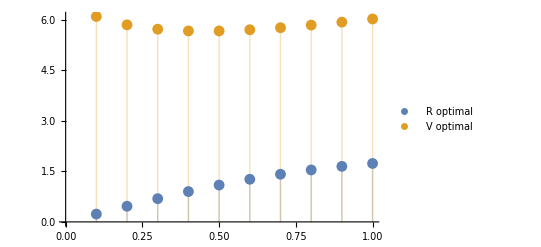
{1.95202,-Graphics-}

```mathematica
AbsoluteTiming[
gammas=Rest[Range[0,1,0.1]];
calcR[lambda_]:= Solve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0,R];
Ropt=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
Vopt=MapThread[V,{gammas,Ropt}]; (* lista V optimais *)
(*gráfico com comportamento de R optimal e V optimal de acordo com gamma*)
ListPlot[{Transpose[{gammas,Ropt}],Transpose[{gammas,Vopt}]},Filling->Axis,PlotLegends->{"R optimal","V optimal"}]
]
```

```mathematica
AbsoluteTiming[
gammas=Rest[Range[0,1,0.1]];
calcR[lambda_]:= NSolve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0,R];
Ropt=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
Vopt=MapThread[V,{gammas,Ropt}]; (* lista V optimais *)
(*gráfico com comportamento de R optimal e V optimal de acordo com gamma*)
ListPlot[{Transpose[{gammas,Ropt}],Transpose[{gammas,Vopt}]},Filling->Axis,PlotLegends->{"R optimal","V optimal"}]
]
```

{0.24671,-Graphics-}

```mathematica
(* espaçamento de 0.05 *)
```

```mathematica
AbsoluteTiming[
gammas=Rest[Range[0,1,0.05]];
calcR[lambda_]:= Solve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0,R];
Ropt=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
Vopt=MapThread[V,{gammas,Ropt}]; (* lista V optimais *)
(*gráfico com comportamento de R optimal e V optimal de acordo com gamma*)
ListPlot[{Transpose[{gammas,Ropt}],Transpose[{gammas,Vopt}]},Filling->Axis,PlotLegends->{"R optimal","V optimal"}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

$Aborted

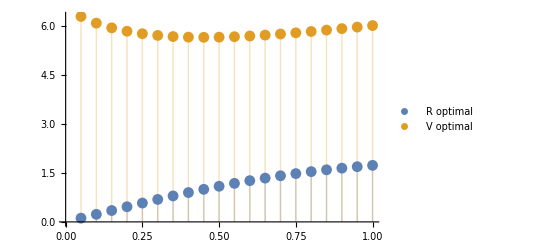
{2.64183,-Graphics-}

```mathematica
AbsoluteTiming[
gammas=Rest[Range[0,1,0.05]];
calcR[lambda_]:= NSolve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0,R];
Ropt=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
Vopt=MapThread[V,{gammas,Ropt}]; (* lista V optimais *)
(*gráfico com comportamento de R optimal e V optimal de acordo com gamma*)
ListPlot[{Transpose[{gammas,Ropt}],Transpose[{gammas,Vopt}]},Filling->Axis,PlotLegends->{"R optimal","V optimal"}]
]
```

```mathematica
(* espaçamento de 0.01 *)
```

```mathematica
AbsoluteTiming[
gammas=Rest[Range[0,1,0.04]];
calcR[lambda_]:= NSolve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0,R];
Ropt=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
Vopt=MapThread[V,{gammas,Ropt}]; (* lista V optimais *)
(*gráfico com comportamento de R optimal e V optimal de acordo com gamma*)
ListPlot[{Transpose[{gammas,Ropt}],Transpose[{gammas,Vopt}]},Filling->Axis,PlotLegends->{"R optimal","V optimal"}]
]
```

$Aborted

```mathematica
(* espaçamento de 0.001 *)
```

```mathematica
AbsoluteTiming[
gammas=Rest[Range[0,1,0.001]];
calcR[lambda_]:= NSolve[F lambda r R^(-1+lambda)-(r+R^lambda)^2==0&&R>0,R];
Ropt=R/.Flatten[Map[calcR,gammas],1]; (* lista R optimais *)
V[gamma_,R_]:=R^gamma/(R^gamma+r)*F-R;
Vopt=MapThread[V,{gammas,Ropt}]; (* lista V optimais *)
(*gráfico com comportamento de R optimal e V optimal de acordo com gamma*)
ListPlot[{Transpose[{gammas,Ropt}],Transpose[{gammas,Vopt}]},Filling->Axis,PlotLegends->{"R optimal","V optimal"}]
]
```